```mathematica
ϵ[r_,mD_,T_]:=-(ⅇ^(-mD r) mD^2)/(4π r)-ⅈ T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(4 π r);
```

### a = -1 (Coulomb)

```mathematica
DSolve[f''[r]+2/r f'[r]==α (ⅇ^(-mD r) mD^2)/r,f[r],r]
```

{{f[r]→(ⅇ^(-mD r) α-C[1])/r+C[2]}}

```mathematica
DSolve[f''[r]+2/r f'[r]==σ T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(4 π r),f[r],r]
```

{{f[r]→C[2]+1/2 (-(2 C[1])/r+(T σ MeijerG[{{3/2},{}},{{3/2,3/2},{0}},(mD^2 r^2)/4])/(2 mD √π r))}}

### a = 2

```mathematica
DSolve[f''[r]-1/r f'[r]==α r^2 ⅇ^(-mD r) mD^2 ,f[r],r]//Simplify
```

{{f[r]→(ⅇ^(-mD r) (3+3 mD r+mD^2 r^2) α)/mD^2+1/2 r^2 C[1]+C[2]}}

```mathematica
DSolve[f''[r]-1/r f'[r]==σ r^2 T mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4] ,f[r],r]//Simplify
```

{{f[r]→1/2 r^2 C[1]+C[2]+(√π r^2 T σ MeijerG[{{1/2},{}},{{3/2,3/2},{-1}},(mD^2 r^2)/4])/mD}}

```mathematica
D[1/2 r^2 C[1]+C[2]+(√π r^2 T σ MeijerG[{{1/2},{}},{{3/2,3/2},{-1}},(mD^2 r^2)/4])/mD,r]
```

r C[1]+(2 √π r T σ MeijerG[{{1/2},{}},{{3/2,3/2},{-1}},(mD^2 r^2)/4])/mD+1/2 mD √π r^3 T σ MeijerG[{{-1,-1/2},{}},{{1/2,1/2},{-2,0}},(mD^2 r^2)/4]

```mathematica
Assuming[{mD∈Reals,mD>0,r∈Reals,r>0,σ∈Reals,σ>0,T∈Reals,T>0},Series[r C[1]+(2 √π r T σ MeijerG[{{1/2},{}},{{3/2,3/2},{-1}},(mD^2 r^2)/4])/mD+1/2 mD √π r^3 T σ MeijerG[{{-1,-1/2},{}},{{1/2,1/2},{-2,0}},(mD^2 r^2)/4],{r,∞,3}]]
```

ⅇ^(-mD r) (ⅇ^(mD r) (C[1] r+(4 T σ)/mD^2+O[1/r]^1)+(-1/2 ⅈ mD π T σ r^3-1/2 ⅈ π T σ r^2-(ⅈ π T σ r)/(2 mD)+O[1/r]^1))

```mathematica
Assuming[{mD∈Reals,mD>0,r∈Reals,r>0,σ∈Reals,σ>0,T∈Reals,T>0},Series[(√π r^2 T σ MeijerG[{{1/2},{}},{{3/2,3/2},{-1}},(mD^2 r^2)/4])/mD,{r,∞,3}]]
```

ⅇ^(-mD r) (ⅇ^(mD r) ((4 T σ r)/mD^2-(32 (T σ))/(mD^4 r)+O[1/r]^2)+(1/2 ⅈ π T σ r^3+(2 ⅈ π T σ r^2)/mD+(9 ⅈ π T σ r)/(2 mD^2)+(9 ⅈ π T σ)/(2 mD^3)+O[1/r]^2))

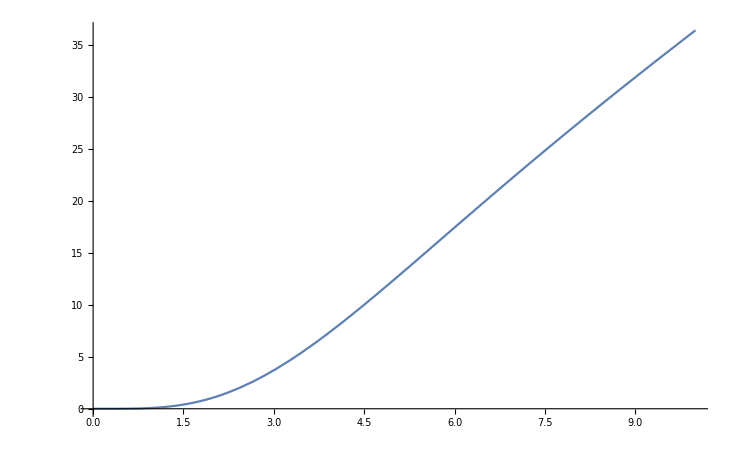

```mathematica
Block[{T=1,σ=1,mD=1},Plot[(√π r^2 T σ MeijerG[{{1/2},{}},{{3/2,3/2},{-1}},(mD^2 r^2)/4])/mD,{r,0,10}]]
```

### a = 3

```mathematica
DSolve[f''[r]-2/r f'[r]==α r^3 ⅇ^(-mD r) mD^2 ,f[r],r]//Simplify
```

{{f[r]→(ⅇ^(-mD r) (8+8 mD r+4 mD^2 r^2+mD^3 r^3) α)/mD^3+1/3 r^3 C[1]+C[2]}}

```mathematica
DSolve[f''[r]-2/r f'[r]==α r^3 T mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4] ,f[r],r]//Simplify
```

{{f[r]→1/3 r^3 C[1]+C[2]+(√π r^3 T α MeijerG[{{-1/2,1/2},{}},{{3/2,3/2},{-3/2,0}},(mD^2 r^2)/4])/mD}}

### a = -2

```mathematica
DSolve[f''[r]+3/r f'[r]==α (ⅇ^(-mD r) mD^2)/r^2 ,f[r],r]//Simplify
```

{{f[r]→C[2]+(ⅇ^(-mD r) (α+mD r α-ⅇ^(mD r) C[1])+mD^2 r^2 α ExpIntegralEi[-mD r])/(2 r^2)}}

```mathematica
DSolve[f''[r]+3/r f'[r]==σ T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/r^2,f[r],r]//Simplify
```

{{f[r]→-C[1]/(2 r^2)+C[2]+(√π T σ MeijerG[{{1/2,2},{}},{{3/2,3/2},{0,1}},(mD^2 r^2)/4])/(mD r^2)}}

### a = 1 (String)

```mathematica
DSolve[f''[r]==α r ⅇ^(-mD r) mD^2 ,f[r],r]//Simplify
```

{{f[r]→(ⅇ^(-mD r) (2+mD r) α+mD (C[1]+r C[2]))/mD}}

```mathematica
DSolve[f''[r]==σ r T mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4] ,f[r],r]//Simplify
```

{{f[r]→C[1]+r C[2]+(√π r T σ MeijerG[{{1/2,1/2},{}},{{3/2,3/2},{-1/2,0}},(mD^2 r^2)/4])/mD}}